# Anharmonic Chains

Reference: Herbert Spohn, Nonlinear fluctuating hydrodynamics for anharmonic chains. J. Stat. Phys. 154, 1191-1227 (2014), arXiv:1305.6412

Square-well potential with alternating masses

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<"anharm_chains_max_dist.m";
```

## Elastic collision

```mathematica
FullSimplify[Solve[{Subscript[m, 1] Subscript[u, 1]+Subscript[m, 2] Subscript[u, 2]==Subscript[m, 1] Subscript[v, 1]+Subscript[m, 2] Subscript[v, 2],1/2 Subscript[m, 1] Subscript[u, 1]^2+1/2 Subscript[m, 2] Subscript[u, 2]^2==1/2 Subscript[m, 1] Subscript[v, 1]^2+1/2 Subscript[m, 2] Subscript[v, 2]^2},{Subscript[v, 1],Subscript[v, 2]}]]
```

{{v_1→u_1,v_2→u_2},{v_1→((m_1-m_2) u_1+2 m_2 u_2)/(m_1+m_2),v_2→(m_1 (2 u_1-u_2)+m_2 u_2)/(m_1+m_2)}}

```mathematica
Subscript[M, mat]={{(Subscript[m, 1]-Subscript[m, 2])/(Subscript[m, 1]+Subscript[m, 2]),(2 Subscript[m, 2])/(Subscript[m, 1]+Subscript[m, 2])},{(2 Subscript[m, 1])/(Subscript[m, 1]+Subscript[m, 2]),-(Subscript[m, 1]-Subscript[m, 2])/(Subscript[m, 1]+Subscript[m, 2])}};
```

```mathematica
Subscript[M, mat]//MatrixForm
```

((m_1-m_2)/(m_1+m_2) | (2 m_2)/(m_1+m_2)
(2 m_1)/(m_1+m_2) | -(m_1-m_2)/(m_1+m_2))

```mathematica
FullSimplify[Eigenvalues[Subscript[M, mat]]]
```

{-1,1}

```mathematica
FullSimplify[{(Subscript[m, 1] Subscript[u, 1]+Subscript[m, 2] Subscript[u, 2])-(Subscript[m, 1] Subscript[v, 1]+Subscript[m, 2] Subscript[v, 2]),(1/2 Subscript[m, 1] Subscript[u, 1]^2+1/2 Subscript[m, 2] Subscript[u, 2]^2)-(1/2 Subscript[m, 1] Subscript[v, 1]^2+1/2 Subscript[m, 2] Subscript[v, 2]^2)}/.{Subscript[v, 1]->First[Subscript[M, mat].{Subscript[u, 1],Subscript[u, 2]}],Subscript[v, 2]->Last[Subscript[M, mat].{Subscript[u, 1],Subscript[u, 2]}]}]
```

{0,0}

```mathematica
(* change in velocity *)
FullSimplify[Subscript[M, mat].{Subscript[u, 1],Subscript[u, 2]}-{Subscript[u, 1],Subscript[u, 2]}]
```

{(2 m_2 (-u_1+u_2))/(m_1+m_2),(2 m_1 (u_1-u_2))/(m_1+m_2)}

```mathematica
(* change in momentum can be expressed in terms of velocity difference *)
FullSimplify[{Subscript[m, 1],Subscript[m, 2]}(Subscript[M, mat].{Subscript[u, 1],Subscript[u, 2]}-{Subscript[u, 1],Subscript[u, 2]})]
(* check momentum conservation *)
FullSimplify[Total[%]]
```

{(2 m_1 m_2 (-u_1+u_2))/(m_1+m_2),(2 m_1 m_2 (u_1-u_2))/(m_1+m_2)}

0

## Import initial data

```mathematica
(* load position data from disk *)
Subscript[r, data,0]=Import["collision_test_field_r0.dat","Real64"]
Length[%]
```

{0.084313,0.110903,0.0401061,0.667195,0.802043,0.0841625,0.816367,0.951639,0.824709,0.63249,0.121946,0.169508,0.64357,0.696474,0.811512,0.0758362}

16

```mathematica
(* average elongation, should be conserved *)
Mean[Subscript[r, data,0]]
```

0.470798

```mathematica
Subscript[q, data,0]=Most[Accumulate[Prepend[Subscript[r, data,0],0]]]
Length[%]
```

{0,0.084313,0.195216,0.235322,0.902517,1.70456,1.78872,2.60509,3.55673,4.38144,5.01393,5.13587,5.30538,5.94895,6.64542,7.45694}

16

```mathematica
(* load momentum data from disk *)
Subscript[p, data,0]=Import["collision_test_field_p0.dat","Real64"]
```

{0.695259,-1.49671,0.404693,-1.0769,0.668085,-2.80978,0.338052,-0.0189182,-0.300148,2.70245,-1.26843,3.56142,0.406422,1.56139,-1.12714,2.3231}

```mathematica
(* expectation value is zero, but not current actual value *)
Mean[Subscript[p, data,0]]
```

0.285178

```mathematica
(* alternating masses *)
Subscript[m, 0,1,val]={1,3};
```

```mathematica
Subscript[mass, val]=Flatten[ConstantArray[Subscript[m, 0,1,val],Length[Subscript[q, data,0]]/2]]
```

{1,3,1,3,1,3,1,3,1,3,1,3,1,3,1,3}

```mathematica
(* square-well potential width *)
Subscript[a, val]=1;
```

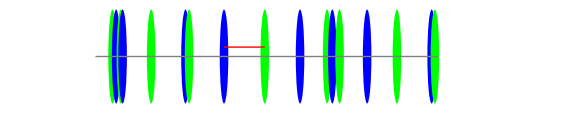

```mathematica
VisualizeField[Accumulate[Prepend[Subscript[r, data,0],0.4]],Append[Subscript[mass, val],First[Subscript[mass, val]]]/Mean[Subscript[m, 0,1,val]],Subscript[a, val],8]
```

```mathematica
(* without taking collisions into account *)
Animate[VisualizeField[Subscript[q, data,0]+0.4+t Subscript[p, data,0]/Subscript[mass, val],Append[Subscript[mass, val],First[Subscript[mass, val]]]/Mean[Subscript[m, 0,1,val]],Subscript[a, val],8],{t,0,10},AnimationRunning->False]
```

## Run simulation

```mathematica
(* example *)
NextCollision[Subscript[r, data,0],Subscript[p, data,0],Subscript[mass, val],Subscript[a, val]]
```

{-1.14549,0.0525183,CollCore,3}

```mathematica
(* example *)
UpdateField[{Subscript[q, data,0],Subscript[p, data,0],0},Total[Subscript[r, data,0]],Subscript[mass, val],Subscript[a, val]];
Differences[First[%]]
```

{0.0215976,0.158358,0.,0.721134,0.717768,0.151105,0.798282,0.936207,0.887781,0.518565,0.250908,0.128506,0.649559,0.609944,0.911376}

```mathematica
Subscript[f, seq]=FieldSequence[{Subscript[q, data,0],Subscript[p, data,0],0},Total[Subscript[r, data,0]],Subscript[mass, val],Subscript[a, val],93];
Length[%]
```

94

```mathematica
(* example *)
Subscript[f, seq]⟦{1,2,-1}⟧
```

{{{0,0.084313,0.195216,0.235322,0.902517,1.70456,1.78872,2.60509,3.55673,4.38144,5.01393,5.13587,5.30538,5.94895,6.64542,7.45694},{0.695259,-1.49671,0.404693,-1.0769,0.668085,-2.80978,0.338052,-0.0189182,-0.300148,2.70245,-1.26843,3.56142,0.406422,1.56139,-1.12714,2.3231},0},{{0.0365138,0.0581114,0.21647,0.21647,0.937603,1.65537,1.80648,2.60476,3.54096,4.42875,4.94731,5.19822,5.32673,5.97628,6.58623,7.49761},{0.695259,-1.49671,-0.740798,0.0685883,0.668085,-2.80978,0.338052,-0.0189182,-0.300148,2.70245,-1.26843,3.56142,0.406422,1.56139,-1.12714,2.3231},0.0525183},{{0.523265,1.27466,1.76272,1.79521,2.59517,3.32657,3.6868,3.88635,3.89392,4.65698,4.87762,4.99122,5.24935,6.08959,7.08959,7.31225},{0.254723,-0.161854,1.66747,-0.430909,1.33554,-3.24347,-0.579858,-1.07413,0.261563,0.141414,1.64439,0.191938,1.38201,1.75272,-0.936131,2.35745},5.17474}}

```mathematica
Interpolation[{Last[#],First[#]}&/@Subscript[f, seq],InterpolationOrder->1]
Animate[VisualizeField[%[t],Subscript[mass, val]/Mean[Subscript[m, 0,1,val]],Subscript[a, val],8],{t,0,3},AnimationRunning->False]
```

InterpolatingFunction[{{0., 5.17474}}, <>]

## Compare with C implementation

```mathematica
CollisionInfo[{q_List,p_List,t_},L_,mass_,a_]:=Module[{r=FieldDifferences[q,L],Δt,type,i},
	{Δt,type,i}=Rest[NextCollision[r,p,mass,a]];{t+Δt,type,i}]
```

```mathematica
(* reference *)
Subscript[coll, ref]=CollisionInfo[AdvanceField[#,Subscript[mass, val],0.0001],Total[Subscript[r, data,0]],Subscript[mass, val],Subscript[a, val]]&/@Subscript[f, seq];
Length[%]
```

94

```mathematica
(* example *)
Subscript[coll, ref]⟦{1,2,-1}⟧
```

{{0.0525183,CollCore,3},{0.0706043,CollCore,1},{5.19268,CollCore,3}}

```mathematica
(* load C implementation results from disk *)
"collision_test_event_";
Subscript[coll, test]=Transpose[{(* event times *)Import[%<>"time.dat","Real64"],(* event types *) Import[%<>"type.dat","Integer32"]/.{0->CollString,1->CollCore},(* particle indices *)Import[%<>"iprt.dat","Integer32"]+1}];
Length[%]
```

94

```mathematica
(* example *)
Subscript[coll, test]⟦{1,2,-1}⟧
```

{{0.0525183,CollCore,3},{0.0706043,CollCore,1},{5.19268,CollCore,3}}

```mathematica
(* compare *)
Norm[Subscript[coll, ref]-Subscript[coll, test]]
```

4.97551×10^-14

```mathematica
(* save reference to disk for comparison *)
"collision_test_ref_event_";
{(* event times *)Export[%<>"time.dat",Subscript[coll, ref]⟦;;,1⟧,"Real64"],(* event types *) Export[%<>"type.dat",Subscript[coll, ref]⟦;;,2⟧/.{CollString->0,CollCore->1},"Integer32"],(* particle indices *)Export[%<>"iprt.dat",Subscript[coll, ref]⟦;;,3⟧-1,"Integer32"]};
```